```mathematica
(*Time duration calculations*)
```

```mathematica
Clear["Global`*"]
Tstart=AbsoluteTime[{2022,7,22,13,47,36}]
Tstop=AbsoluteTime[{2022,7,29,9,45,00}]
duration=N[(Tstop-Tstart)]
```

3867486456

3868076700

590244.

```mathematica
(*SOURCE: 60Co*)
```

3867824011

3867916817

92806.

2.17035×10^8

3.46568×10^9

Activity  (Bq) 37350.5

Duration (s) 92806.

Activity Sum  3.46635×10^9

Int Sum  3465676423.

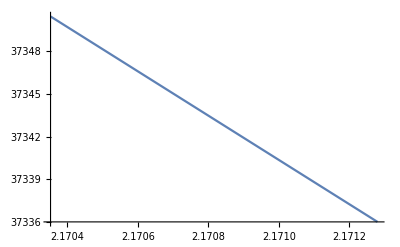

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2015,9,9,12,00}];
TH2=1925.28*24*3600;(*NNDC, days -> seconds*)
A0=92.27*10^3;(*Bq*)
λ:=Log[2]/TH2;


Tstart=AbsoluteTime[{2022,7,26,11,33,31}]
Tstop=AbsoluteTime[{2022,7,27,13,20,17}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",ActivitySum]
Print["Int Sum  ",DecimalForm[SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]
```

```mathematica
(*SOURCE: 137Cs*)
```

3867134027

3867155760

21733.

2.16345×10^8

6.72398×10^9

Activity  (Bq) 309393.

Duration (s) 21733.

Activity Sum  5.72215×10^9

Int Sum  5722108282.

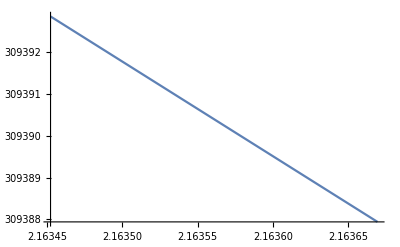

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2015,9,9,12,00}];
TH2=30.07*365*24*3600;(*NNDC, days -> seconds*)
A0=362.4*10^3;(*Bq*)
λ:=Log[2]/TH2;
Nbranching=0.851;

Tstart=AbsoluteTime[{2022,07,18,11,53,47}]
Tstop=AbsoluteTime[{2022,07,18,17,56,00}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",Nbranching*ActivitySum]dom_115_eff.eps
Print["Int Sum  ",DecimalForm[Nbranching*SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]
```

```mathematica
(*SOURCE: 54Mn*)
```

3845618755

3845619347

592.

2.203×10^7

1.73493×10^8

Activity  (Bq) 293065.

Duration (s) 592.

Activity Sum  1.73495×10^8

Int Sum  173493300.

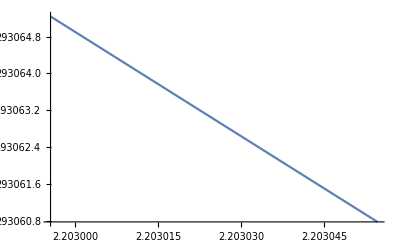

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2021,03,01,12,00}];
TH2=312.2*24*3600;(*NNDC, days -> seconds*)
A0=516.2*10^3;(*Bq*)
λ:=Log[2]/TH2;


Tstart=AbsoluteTime[{2021,11,11,11,25,55}]
Tstop=AbsoluteTime[{2021,11,11,11,35,47}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",ActivitySum]
Print["Int Sum  ",DecimalForm[SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]
```

```mathematica
(*SOURCE: 133Ba*)
```

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2021,03,01,12,00}];
TH2=10.551*365*24*3600;(*NNDC, seconds*)
A0=3.9*10^3;(*Bq*)
λ:=Log[2]/TH2;


Tstart=AbsoluteTime[{2021,11,11,12,26,10}]
Tstop=AbsoluteTime[{2021,11,11,12,40,13}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",ActivitySum]
Print["Int Sum  ",DecimalForm[SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]
```

3845622370

3845623213

843.

2.20336×10^7

3.1402×10^6

Activity  (Bq) 3725.04

Duration (s) 843.

Activity Sum  3.14021×10^6

Int Sum  3140204.

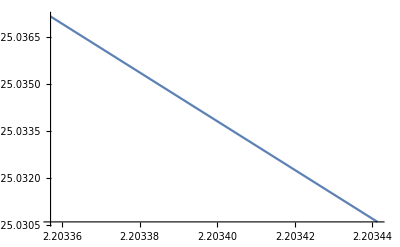
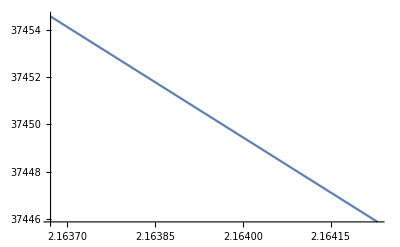
```mathematica
-Graphics--Graphics-dom_115_eff.eps
```

```mathematica
(*SOURCE: 22Na*)
```

3867134027

3867155760

21733.

2.16345×10^8

3.85084×10^8

Activity  (Bq) 17720.5

Duration (s) 21733.

Activity Sum  3.85119×10^8

Int Sum  385083587.

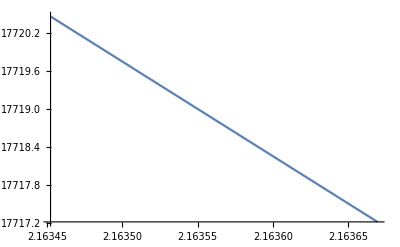

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2015,09,09,12,00}];
TH2=2.6019*365*24*3600;(*NNDC, seconds*)
A0=110.2*10^3;(*Bq*)
λ:=Log[2]/TH2;
Nbranching=0.99944;

Tstart=AbsoluteTime[{2022,07,18,11,53,47}]
Tstop=AbsoluteTime[{2022,07,18,17,56,00}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",ActivitySum]
Print["Int Sum  ",DecimalForm[SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]
```

```mathematica
(*SOURCE: 152Eu*)
```

3868340300

3868355100

14800.

2.17552×10^8

5.65002×10^9

Activity  (Bq) 381763.

Duration (s) 14800.

Activity Sum  5.65009×10^9

Int Sum  5650018617.

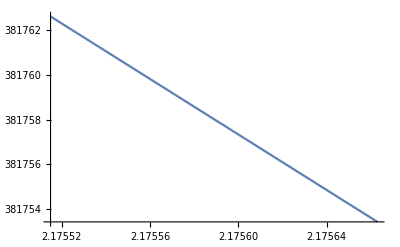

4.26903×10^8

1.62366×10^-9

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2015,9,9,12,00}];
TH2=13.537*365*24*3600;(*NNDC, days -> seconds*)
A0=543.5*10^3;(*Bq*)
λ:=Log[2]/TH2


Tstart=AbsoluteTime[{2022,8,1,10,58,20}]
Tstop=AbsoluteTime[{2022,8,1,15,05,00}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",ActivitySum]
Print["Int Sum  ",DecimalForm[SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]

TH2
λ
```